## Project 10 - Javier Salazar 1001144647.

1.  Let   X_1(t) = 1 + X(t)  be the Brownian motion starting at 1 and  X_2(t) = 2 + Y(t) be the Brownian motion starting at 2, where  X(t) and Y(t) are independent standard Brownian motions started at x = 0 at time t = 0.

(a)  Simulate n = 10,000 trials of the process  X_1(t) and X_2(t)  for  0 ≤ t ≤ 1

(b)  Find the frequency of  | X_2(1) - X_1(1) | ≤ 1  and compare with the exact P (| X_2(1) - X_1(1) | ≤ 1)
       Hint.   X_2(1) - X_1(1) ~  N(μ, σ^2) = N(1, 2)
       
(c)  Plot a sample of  X_1(t),  X_2(t), together on a single graph  for  0 ≤ t ≤ 1,  for which  | X_2(1) - X_1(1) | ≤ 1

```mathematica
n=10000;x=0;a=-1;b=1;t=1;h=.005;d=√h;  counts=0;m=t/h;
Do[ s=1;
 Do[s=s+Random[NormalDistribution[0,d]]-Random[NormalDistribution[0,d]],{m}];  
 If [ a≤s≤b, counts= counts+1], 
{n}];
Print["frequency(X_2(t)- X_1(t) belongs to [",a,"," ,b,"]) = ",counts/n//N]
Print["exact probability = ",NIntegrate[1/(2 √π)ⅇ^(- (1-x)^2/4),{x,a,b}]];
```

frequency(X_2(t)- X_1(t) belongs to [-1,1]) = 0.419

exact probability = 0.42135

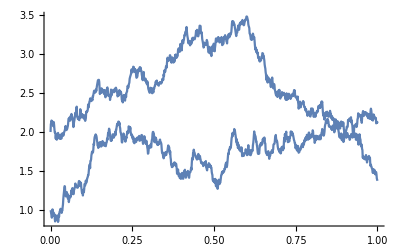

```mathematica
BrownianMotion[x_,t_,h_]:=Module[{d=√h,m=t/h},
g=Table[Random[NormalDistribution[0,d]],{m}];sums=FoldList[Plus,0,g];
Table[X[i*h]=sums[[i+1]],{i,0,m}];
brown=Table[{i*h,x+X[i*h]},{i,0,m}];
ListLinePlot[brown,Joined->True]];
g1=BrownianMotion[1,1,.001];
g2=BrownianMotion[2,1,.001];
Show[g1,g2,PlotRange->All]
```

2.  Let  Y_x^y(s) be the Brownian Bridge for  0 ≤ s ≤ t = 2, and x = 0, y = 1. 

 Simulate n = 10,000 trials of the process  Y_0^1(1) while counting the frequency of  Y_0^1(1) landing in [0,2],
 for  (a)  h = .005, and  (b)  h =.001 and Plot a single realization in (a) and (b) that lands in [0,2]
      
(c)  compare the frequencies from (a) and (b)  with the exact probability  P( 0 ≤ Y_0^1(1)   ≤ 2 )

(d)  repeat (a)-(c)  for  n = 40,000

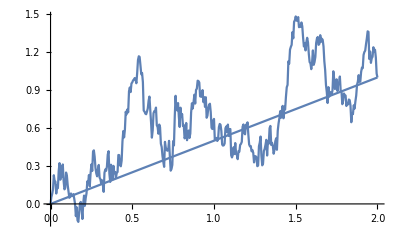

```mathematica
BrownianBridge[x_,y_,t_,h_]:=Module[{d=√h,m=t/h},
g=Table[Random[NormalDistribution[0,d]],{m}];
sums=FoldList[Plus,0,g];Table[X[i*h]=sums[[i+1]],{i,0,m}];
bridgeMean=Table[{i*h,x-(i/m)*(x-y)},{i,0,m}];
bridge=Table[{i*h,x+X[i*h]-(i/m)*(X[m*h]+x-y)},{i,0,m}];
g1=ListPlot[bridgeMean,Joined->True,DisplayFunction->Identity];
g2=ListPlot[bridge,Joined->True,DisplayFunction->Identity];
Show[g1,g2,PlotRange->All, DisplayFunction->$DisplayFunction]];
BrownianBridge[0,1,2,.005]
```

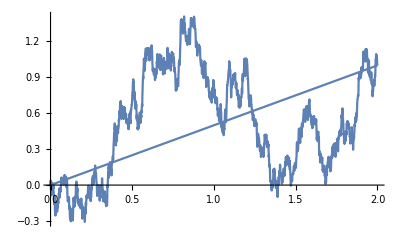

```mathematica
BrownianBridge[x_,y_,t_,h_]:=Module[{d=√h,m=t/h},
g=Table[Random[NormalDistribution[0,d]],{m}];
sums=FoldList[Plus,0,g];Table[X[i*h]=sums[[i+1]],{i,0,m}];
bridgeMean=Table[{i*h,x-(i/m)*(x-y)},{i,0,m}];
bridge=Table[{i*h,x+X[i*h]-(i/m)*(X[m*h]+x-y)},{i,0,m}];
g1=ListPlot[bridgeMean,Joined->True,DisplayFunction->Identity];
g2=ListPlot[bridge,Joined->True,DisplayFunction->Identity];
Show[g1,g2,PlotRange->All, DisplayFunction->$DisplayFunction]];
BrownianBridge[0,1,2,.001]
```

```mathematica
BrownianBridge[x_,y_,t_,h_]:=Module[{d=√h,m=t/h},
g=Table[Random[NormalDistribution[0,d]],{m}];
sums=FoldList[Plus,0,g];Table[X[i*h]=sums[[i+1]],{i,0,m}];
bridge=Table[x+X[i*h]-(i/m)*(X[m*h]+x-y),{i,0,m}];];
n=10000;x=0;y=1;a=0;b=2;t=2;h=.005;d=√h; counts=0;m=t/h;
For[i=1,i<n+1,i++,BrownianBridge[x,y,t,h];If[0≤ bridge[[m/2+1]]≤ 2,counts=counts+1,counts=counts]]
Print["frequency(X_x(t) belongs to [",a,"," ,b,"]) = ",counts/n//N]
Print["exact probability = ",NIntegrate[1/(√π)ⅇ^(- (u-1/2)^2),{u,a,b}]];
```

frequency(X_x(t) belongs to [0,2]) = 0.7429

exact probability = 0.743303

```mathematica
BrownianBridge[x_,y_,t_,h_]:=Module[{d=√h,m=t/h},
g=Table[Random[NormalDistribution[0,d]],{m}];
sums=FoldList[Plus,0,g];Table[X[i*h]=sums[[i+1]],{i,0,m}];
bridge=Table[x+X[i*h]-(i/m)*(X[m*h]+x-y),{i,0,m}];];
n=10000;x=0;y=1;a=0;b=2;t=2;h=.001;d=√h; counts=0;m=t/h;
For[i=1,i<n+1,i++,BrownianBridge[x,y,t,h];If[0≤ bridge[[m/2+1]]≤ 2,counts=counts+1,counts=counts]]
Print["frequency(X_x(t) belongs to [",a,"," ,b,"]) = ",counts/n//N]
Print["exact probability = ",NIntegrate[1/(√π)ⅇ^(- (u-1/2)^2),{u,a,b}]];
```

frequency(X_x(t) belongs to [0,2]) = 0.7437

exact probability = 0.743303

```mathematica
BrownianBridge[x_,y_,t_,h_]:=Module[{d=√h,m=t/h},
g=Table[Random[NormalDistribution[0,d]],{m}];
sums=FoldList[Plus,0,g];Table[X[i*h]=sums[[i+1]],{i,0,m}];
bridge=Table[x+X[i*h]-(i/m)*(X[m*h]+x-y),{i,0,m}];];
n=40000;x=0;y=1;a=0;b=2;t=2;h=.005;d=√h; counts=0;m=t/h;
For[i=1,i<n+1,i++,BrownianBridge[x,y,t,h];If[0≤ bridge[[m/2+1]]≤ 2,counts=counts+1,counts=counts]]
Print["frequency(X_x(t) belongs to [",a,"," ,b,"]) = ",counts/n//N]
Print["exact probability = ",NIntegrate[1/(√π)ⅇ^(- (u-1/2)^2),{u,a,b}]];
```

frequency(X_x(t) belongs to [0,2]) = 0.7402

exact probability = 0.743303

```mathematica
BrownianBridge[x_,y_,t_,h_]:=Module[{d=√h,m=t/h},
g=Table[Random[NormalDistribution[0,d]],{m}];
sums=FoldList[Plus,0,g];Table[X[i*h]=sums[[i+1]],{i,0,m}];
bridge=Table[x+X[i*h]-(i/m)*(X[m*h]+x-y),{i,0,m}];];
n=40000;x=0;y=1;a=0;b=2;t=2;h=.001;d=√h; counts=0;m=t/h;
For[i=1,i<n+1,i++,BrownianBridge[x,y,t,h];If[0≤ bridge[[m/2+1]]≤ 2,counts=counts+1,counts=counts]]
Print["frequency(X_x(t) belongs to [",a,"," ,b,"]) = ",counts/n//N]
Print["exact probability = ",NIntegrate[1/(√π)ⅇ^(- (u-1/2)^2),{u,a,b}]];
```

frequency(X_x(t) belongs to [0,2]) = 0.7437

exact probability = 0.743303

3.  Let  S(t) = ⅇ^(x + μ t+σ X(t)) = s_0 ⅇ^(μ t  +σ X(t)) with  s_0= S(0) = ⅇ^x, be the Geometric Brownian Motion with
     x = 0, μ =.10, σ =.3,  0 ≤  t (in years). This means the 1 share of Stock has price $1 at time 0, with
     average annual return 10%  and  30% volatility. 
     
     (a)  Find the exact probability that the stock price after 1 year is at least $1.15.
     
     (b)   Simulate n = 10,000 trials of the process S(1) while counting the frequency of  S(1) ≥ 1.15,
            for  h =.001 and plot a single realization that is at least 1.15  after one year.
            
    (c)  compare the frequency  (b)  with the exact probability P( 1.15 ≤ S(1) )  found in (a)

```mathematica
BrownianGeometric[x0_,μ_,σ_,t_,h_]:=Module[{d=√h,m=t/h},
g=Table[Random[NormalDistribution[0,d]],{m}];
sums=FoldList[Plus,0,g];Table[X[i*h]=sums[[i+1]],{i,0,m}];
geometric=Table[x0*ⅇ^(μ *i/m+σ*X[i*h]),{i,0,m}];];
n=10000;x=1;μ=.1;σ=.3;t=1;h=.001;d=√h;  counts=0;m=t/h;
For[i=1,i<n+1,i++,BrownianGeometric[x,μ,σ,t,h];If[ geometric[[m+1]]≥ 1.15,counts=counts+1,counts=counts]]
Print["frequency S(1) >= 1.15 = ",counts/n//N]
(Log[1.15]-.1)/.3//N;
Print["exact probability = ",NIntegrate[1/(.3*√(2π))ⅇ^(- (x-.1)^2/(2*.3^2)),{x,0.13254,Infinity}]];
```

frequency S(1) >= 1.15 = 0.4412

exact probability = 0.456813

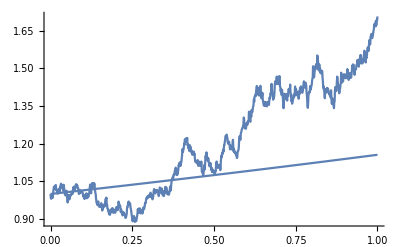

```mathematica
BrownianGeometric[x0_,μ_,σ_,t_,h_]:=Module[{d=√h,m=t/h},
g=Table[Random[NormalDistribution[0,d]],{m}];
sums=FoldList[Plus,0,g];Table[X[i*h]=sums[[i+1]],{i,0,m}];
geometric=Table[{i*h,x0*ⅇ^(μ *i/m+σ*X[i*h])},{i,0,m}];
drift=Table[{i*h,x0*ⅇ^((i/m) * (μ +σ^2/2))},{i,0,m}];
g1=ListPlot[geometric,Joined->True,DisplayFunction->Identity];
g2=ListPlot[drift,Joined->True,DisplayFunction->Identity];
Show[g1,g2,PlotRange->All,DisplayFunction->$DisplayFunction]];
BrownianGeometric[x,μ,σ,t,h]
```